# ABS Model with no Wake

## Solve for time (theta)-dependent Fourier Coefficients

-Graphics-

-Graphics-

```mathematica
$Assumptions=q∈Reals
size = 20;
matrix1 = (1/I)*Table[(n-q/2)*KroneckerDelta[n,m]+(q/2)*KroneckerDelta[-n,m],{n,-size,size,1},{m,-size,size,1}];
```

q∈ℝ

```mathematica
eigenvalues1 = Eigenvalues[matrix1];
eigenvectors1 = Eigenvectors[matrix1];
```

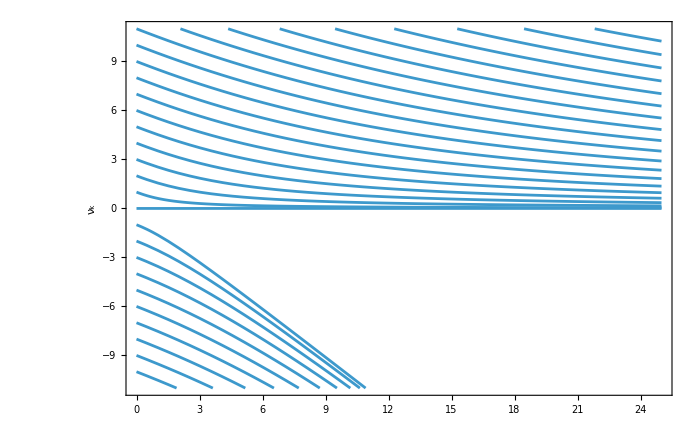

```mathematica
Plot[-Im[eigenvalues1],{q,0,25},PlotRange->{{0,25},{-11,11}},
FrameLabel->{Style["",45,Black],Style[,45,Black]},
FrameStyle->Black,Frame->True,ImageSize->700,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30}]
```

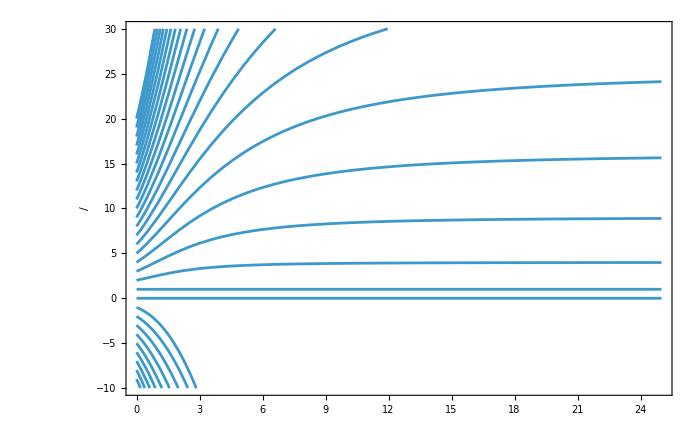

```mathematica
Plot[Im[eigenvalues1]/Im[eigenvalues1[[2]]],{q,0,25},PlotRange->{{0,25},{-10,30}},
FrameLabel->{ Style["",45,Black],Style[" / ",45,Black]},
FrameStyle->Black,Frame->True,ImageSize->700,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30}]
```

```mathematica
order = Ordering[-Im[eigenvalues1]/.q->0];
ks = Im[SortBy[eigenvalues1/.q->0,Im]];
-eigenvalues1[[order]]
```

{-1/2 ⅈ (q+√(1600+q^2)),-1/2 ⅈ (q+√(1444+q^2)),-1/2 ⅈ (q+√(1296+q^2)),-1/2 ⅈ (q+√(1156+q^2)),-1/2 ⅈ (q+√(1024+q^2)),-1/2 ⅈ (q+√(900+q^2)),-1/2 ⅈ (q+√(784+q^2)),-1/2 ⅈ (q+√(676+q^2)),-1/2 ⅈ (q+√(576+q^2)),-1/2 ⅈ (q+√(484+q^2)),-1/2 ⅈ (q+√(400+q^2)),-1/2 ⅈ (q+√(324+q^2)),-1/2 ⅈ (q+√(256+q^2)),-1/2 ⅈ (q+√(196+q^2)),-1/2 ⅈ (q+√(144+q^2)),-1/2 ⅈ (q+√(100+q^2)),-1/2 ⅈ (q+√(64+q^2)),-1/2 ⅈ (q+√(36+q^2)),-1/2 ⅈ (q+√(16+q^2)),-1/2 ⅈ (q+√(4+q^2)),0,-1/2 ⅈ (q-√(4+q^2)),-1/2 ⅈ (q-√(16+q^2)),-1/2 ⅈ (q-√(36+q^2)),-1/2 ⅈ (q-√(64+q^2)),-1/2 ⅈ (q-√(100+q^2)),-1/2 ⅈ (q-√(144+q^2)),-1/2 ⅈ (q-√(196+q^2)),-1/2 ⅈ (q-√(256+q^2)),-1/2 ⅈ (q-√(324+q^2)),-1/2 ⅈ (q-√(400+q^2)),-1/2 ⅈ (q-√(484+q^2)),-1/2 ⅈ (q-√(576+q^2)),-1/2 ⅈ (q-√(676+q^2)),-1/2 ⅈ (q-√(784+q^2)),-1/2 ⅈ (q-√(900+q^2)),-1/2 ⅈ (q-√(1024+q^2)),-1/2 ⅈ (q-√(1156+q^2)),-1/2 ⅈ (q-√(1296+q^2)),-1/2 ⅈ (q-√(1444+q^2)),-1/2 ⅈ (q-√(1600+q^2))}

## Solve for ABS Eigenfunctions given ν_k

-Graphics-

-Graphics-

```mathematica
matrices = Table[{{-I*Pi*q/2-Pi*Subscript[ν, k],I*q*Pi/2},{-I*q*Pi/2,I*Pi*q/2+Pi*Subscript[ν, k]}},{Subscript[ν, k],-eigenvalues1[[order]]}];
```

```mathematica
eigenvalues2 = Table[FullSimplify[Eigenvalues[mi]],{mi,matrices}];
Dimensions[eigenvalues2]
eigenvectors2 = Table[FullSimplify[Eigenvectors[mi]],{mi,matrices}];
Dimensions[eigenvectors2]
```

{41,2}

{41,2,2}

```mathematica
solutions2 = FullSimplify[Table[eigenvectors2[[i]]*Exp[eigenvalues2[[i]]*s],{i,Dimensions[eigenvalues2][[1]]}]];
Dimensions[solutions2]
```

{41,2,2}

```mathematica
as = Table[Solve[(a*solutioni[[1]][[1]]+b*solutioni[[2]][[1]]==a*solutioni[[1]][[2]]+b*solutioni[[2]][[2]])/.s->0,{a}],{solutioni,solutions2}];
Dimensions[as]
```

{41,1}

```mathematica
eigensolutions2 = Table[Collect[ExpToTrig[Check[(a*solutions2[[i]][[1]][[1]]+b*solutions2[[i]][[2]][[1]])/.as[[i]][[1]][[1]],1]],{Cos[_],Sin[_]}],{i,Length[as]}];
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
coefficients2= Table[Check[Coefficient[eigensolutions2[[i]],{Cos[Abs[ks[[i]]]*Pi*s],Sin[Abs[ks[[i]]]*Pi*s]}],{1,1}],{i,Length[ks]}];
```

Coefficient::ivar: 1 is not a valid variable.

Coefficient::ivar: 0 is not a valid variable.

```mathematica
xkplus = Table[FullSimplify[eigensolutions2[[i]]/coefficients2[[i]][[1]]],{i,Length[eigensolutions2]}]
xkminus = FullSimplify[Re[xkplus]-I*Im[xkplus],Assumptions->{q∈Reals,s∈Reals}]
```

{Cos[20 π s]+1/40 ⅈ (q+√(1600+q^2)) Sin[20 π s],Cos[19 π s]+1/38 ⅈ (q+√(1444+q^2)) Sin[19 π s],Cos[18 π s]+1/36 ⅈ (q+√(1296+q^2)) Sin[18 π s],Cos[17 π s]+1/34 ⅈ (q+√(1156+q^2)) Sin[17 π s],Cos[16 π s]+1/32 ⅈ (q+√(1024+q^2)) Sin[16 π s],Cos[15 π s]+1/30 ⅈ (q+√(900+q^2)) Sin[15 π s],Cos[14 π s]+1/28 ⅈ (q+√(784+q^2)) Sin[14 π s],Cos[13 π s]+1/26 ⅈ (q+√(676+q^2)) Sin[13 π s],Cos[12 π s]+1/24 ⅈ (q+√(576+q^2)) Sin[12 π s],Cos[11 π s]+1/22 ⅈ (q+√(484+q^2)) Sin[11 π s],Cos[10 π s]+1/20 ⅈ (q+√(400+q^2)) Sin[10 π s],Cos[9 π s]+1/18 ⅈ (q+√(324+q^2)) Sin[9 π s],Cos[8 π s]+1/16 ⅈ (q+√(256+q^2)) Sin[8 π s],Cos[7 π s]+1/14 ⅈ (q+√(196+q^2)) Sin[7 π s],Cos[6 π s]+1/12 ⅈ (q+√(144+q^2)) Sin[6 π s],Cos[5 π s]+1/10 ⅈ (q+√(100+q^2)) Sin[5 π s],Cos[4 π s]+1/8 ⅈ (q+√(64+q^2)) Sin[4 π s],Cos[3 π s]+1/6 ⅈ (q+√(36+q^2)) Sin[3 π s],Cos[2 π s]+1/4 ⅈ (q+√(16+q^2)) Sin[2 π s],Cos[π s]+1/2 ⅈ (q+√(4+q^2)) Sin[π s],1,Cos[π s]-1/2 ⅈ (-q+√(4+q^2)) Sin[π s],Cos[2 π s]-1/4 ⅈ (-q+√(16+q^2)) Sin[2 π s],Cos[3 π s]-1/6 ⅈ (-q+√(36+q^2)) Sin[3 π s],Cos[4 π s]-1/8 ⅈ (-q+√(64+q^2)) Sin[4 π s],Cos[5 π s]-1/10 ⅈ (-q+√(100+q^2)) Sin[5 π s],Cos[6 π s]-1/12 ⅈ (-q+√(144+q^2)) Sin[6 π s],Cos[7 π s]-1/14 ⅈ (-q+√(196+q^2)) Sin[7 π s],Cos[8 π s]-1/16 ⅈ (-q+√(256+q^2)) Sin[8 π s],Cos[9 π s]-1/18 ⅈ (-q+√(324+q^2)) Sin[9 π s],Cos[10 π s]-1/20 ⅈ (-q+√(400+q^2)) Sin[10 π s],Cos[11 π s]-1/22 ⅈ (-q+√(484+q^2)) Sin[11 π s],Cos[12 π s]-1/24 ⅈ (-q+√(576+q^2)) Sin[12 π s],Cos[13 π s]-1/26 ⅈ (-q+√(676+q^2)) Sin[13 π s],Cos[14 π s]-1/28 ⅈ (-q+√(784+q^2)) Sin[14 π s],Cos[15 π s]-1/30 ⅈ (-q+√(900+q^2)) Sin[15 π s],Cos[16 π s]-1/32 ⅈ (-q+√(1024+q^2)) Sin[16 π s],Cos[17 π s]-1/34 ⅈ (-q+√(1156+q^2)) Sin[17 π s],Cos[18 π s]-1/36 ⅈ (-q+√(1296+q^2)) Sin[18 π s],Cos[19 π s]-1/38 ⅈ (-q+√(1444+q^2)) Sin[19 π s],Cos[20 π s]-1/40 ⅈ (-q+√(1600+q^2)) Sin[20 π s]}

{Cos[20 π s]-1/40 ⅈ (q+√(1600+q^2)) Sin[20 π s],Cos[19 π s]-1/38 ⅈ (q+√(1444+q^2)) Sin[19 π s],Cos[18 π s]-1/36 ⅈ (q+√(1296+q^2)) Sin[18 π s],Cos[17 π s]-1/34 ⅈ (q+√(1156+q^2)) Sin[17 π s],Cos[16 π s]-1/32 ⅈ (q+√(1024+q^2)) Sin[16 π s],Cos[15 π s]-1/30 ⅈ (q+√(900+q^2)) Sin[15 π s],Cos[14 π s]-1/28 ⅈ (q+√(784+q^2)) Sin[14 π s],Cos[13 π s]-1/26 ⅈ (q+√(676+q^2)) Sin[13 π s],Cos[12 π s]-1/24 ⅈ (q+√(576+q^2)) Sin[12 π s],Cos[11 π s]-1/22 ⅈ (q+√(484+q^2)) Sin[11 π s],Cos[10 π s]-1/20 ⅈ (q+√(400+q^2)) Sin[10 π s],Cos[9 π s]-1/18 ⅈ (q+√(324+q^2)) Sin[9 π s],Cos[8 π s]-1/16 ⅈ (q+√(256+q^2)) Sin[8 π s],Cos[7 π s]-1/14 ⅈ (q+√(196+q^2)) Sin[7 π s],Cos[6 π s]-1/12 ⅈ (q+√(144+q^2)) Sin[6 π s],Cos[5 π s]-1/10 ⅈ (q+√(100+q^2)) Sin[5 π s],Cos[4 π s]-1/8 ⅈ (q+√(64+q^2)) Sin[4 π s],Cos[3 π s]-1/6 ⅈ (q+√(36+q^2)) Sin[3 π s],Cos[2 π s]-1/4 ⅈ (q+√(16+q^2)) Sin[2 π s],Cos[π s]-1/2 ⅈ (q+√(4+q^2)) Sin[π s],1,Cos[π s]+1/2 ⅈ (-q+√(4+q^2)) Sin[π s],Cos[2 π s]+1/4 ⅈ (-q+√(16+q^2)) Sin[2 π s],Cos[3 π s]+1/6 ⅈ (-q+√(36+q^2)) Sin[3 π s],Cos[4 π s]+1/8 ⅈ (-q+√(64+q^2)) Sin[4 π s],Cos[5 π s]+1/10 ⅈ (-q+√(100+q^2)) Sin[5 π s],Cos[6 π s]+1/12 ⅈ (-q+√(144+q^2)) Sin[6 π s],Cos[7 π s]+1/14 ⅈ (-q+√(196+q^2)) Sin[7 π s],Cos[8 π s]+1/16 ⅈ (-q+√(256+q^2)) Sin[8 π s],Cos[9 π s]+1/18 ⅈ (-q+√(324+q^2)) Sin[9 π s],Cos[10 π s]+1/20 ⅈ (-q+√(400+q^2)) Sin[10 π s],Cos[11 π s]+1/22 ⅈ (-q+√(484+q^2)) Sin[11 π s],Cos[12 π s]+1/24 ⅈ (-q+√(576+q^2)) Sin[12 π s],Cos[13 π s]+1/26 ⅈ (-q+√(676+q^2)) Sin[13 π s],Cos[14 π s]+1/28 ⅈ (-q+√(784+q^2)) Sin[14 π s],Cos[15 π s]+1/30 ⅈ (-q+√(900+q^2)) Sin[15 π s],Cos[16 π s]+1/32 ⅈ (-q+√(1024+q^2)) Sin[16 π s],Cos[17 π s]+1/34 ⅈ (-q+√(1156+q^2)) Sin[17 π s],Cos[18 π s]+1/36 ⅈ (-q+√(1296+q^2)) Sin[18 π s],Cos[19 π s]+1/38 ⅈ (-q+√(1444+q^2)) Sin[19 π s],Cos[20 π s]+1/40 ⅈ (-q+√(1600+q^2)) Sin[20 π s]}

```mathematica
FullSimplify[Conjugate[xkplus],Assumptions->{s∈Reals,q∈Reals}]
```

{Cos[20 π s]-1/40 ⅈ (q+√(1600+q^2)) Sin[20 π s],Cos[19 π s]-1/38 ⅈ (q+√(1444+q^2)) Sin[19 π s],Cos[18 π s]-1/36 ⅈ (q+√(1296+q^2)) Sin[18 π s],Cos[17 π s]-1/34 ⅈ (q+√(1156+q^2)) Sin[17 π s],Cos[16 π s]-1/32 ⅈ (q+√(1024+q^2)) Sin[16 π s],Cos[15 π s]-1/30 ⅈ (q+√(900+q^2)) Sin[15 π s],Cos[14 π s]-1/28 ⅈ (q+√(784+q^2)) Sin[14 π s],Cos[13 π s]-1/26 ⅈ (q+√(676+q^2)) Sin[13 π s],Cos[12 π s]-1/24 ⅈ (q+√(576+q^2)) Sin[12 π s],Cos[11 π s]-1/22 ⅈ (q+√(484+q^2)) Sin[11 π s],Cos[10 π s]-1/20 ⅈ (q+√(400+q^2)) Sin[10 π s],Cos[9 π s]-1/18 ⅈ (q+√(324+q^2)) Sin[9 π s],Cos[8 π s]-1/16 ⅈ (q+√(256+q^2)) Sin[8 π s],Cos[7 π s]-1/14 ⅈ (q+√(196+q^2)) Sin[7 π s],Cos[6 π s]-1/12 ⅈ (q+√(144+q^2)) Sin[6 π s],Cos[5 π s]-1/10 ⅈ (q+√(100+q^2)) Sin[5 π s],Cos[4 π s]-1/8 ⅈ (q+√(64+q^2)) Sin[4 π s],Cos[3 π s]-1/6 ⅈ (q+√(36+q^2)) Sin[3 π s],Cos[2 π s]-1/4 ⅈ (q+√(16+q^2)) Sin[2 π s],Cos[π s]-1/2 ⅈ (q+√(4+q^2)) Sin[π s],1,Cos[π s]+1/2 ⅈ (-q+√(4+q^2)) Sin[π s],Cos[2 π s]+1/4 ⅈ (-q+√(16+q^2)) Sin[2 π s],Cos[3 π s]+1/6 ⅈ (-q+√(36+q^2)) Sin[3 π s],Cos[4 π s]+1/8 ⅈ (-q+√(64+q^2)) Sin[4 π s],Cos[5 π s]+1/10 ⅈ (-q+√(100+q^2)) Sin[5 π s],Cos[6 π s]+1/12 ⅈ (-q+√(144+q^2)) Sin[6 π s],Cos[7 π s]+1/14 ⅈ (-q+√(196+q^2)) Sin[7 π s],Cos[8 π s]+1/16 ⅈ (-q+√(256+q^2)) Sin[8 π s],Cos[9 π s]+1/18 ⅈ (-q+√(324+q^2)) Sin[9 π s],Cos[10 π s]+1/20 ⅈ (-q+√(400+q^2)) Sin[10 π s],Cos[11 π s]+1/22 ⅈ (-q+√(484+q^2)) Sin[11 π s],Cos[12 π s]+1/24 ⅈ (-q+√(576+q^2)) Sin[12 π s],Cos[13 π s]+1/26 ⅈ (-q+√(676+q^2)) Sin[13 π s],Cos[14 π s]+1/28 ⅈ (-q+√(784+q^2)) Sin[14 π s],Cos[15 π s]+1/30 ⅈ (-q+√(900+q^2)) Sin[15 π s],Cos[16 π s]+1/32 ⅈ (-q+√(1024+q^2)) Sin[16 π s],Cos[17 π s]+1/34 ⅈ (-q+√(1156+q^2)) Sin[17 π s],Cos[18 π s]+1/36 ⅈ (-q+√(1296+q^2)) Sin[18 π s],Cos[19 π s]+1/38 ⅈ (-q+√(1444+q^2)) Sin[19 π s],Cos[20 π s]+1/40 ⅈ (-q+√(1600+q^2)) Sin[20 π s]}

```mathematica
ints=FullSimplify[Table[(1/2)*Integrate[FullSimplify[(Abs[xkplus[[i]]])^2+(Abs[xkminus[[i]]])^2,Assumptions->{q∈Reals,s∈Reals}],{s,0,1}],{i,Length[xkplus]}]];
cks =FullSimplify[Sqrt[1/ints]];
```

```mathematica
ckstheo = FullSimplify[Sqrt[2/(1+(-Im[eigenvalues1[[order]]]/Abs[ks])^2)],Assumptions->{q∈Reals}]/.Indeterminate->1.
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{40/(√(1600+q (q+√(1600+q^2)))),38/(√(1444+q (q+√(1444+q^2)))),36/(√(1296+q (q+√(1296+q^2)))),34/(√(1156+q (q+√(1156+q^2)))),32/(√(1024+q (q+√(1024+q^2)))),30/(√(900+q (q+√(900+q^2)))),28/(√(784+q (q+√(784+q^2)))),26/(√(676+q (q+√(676+q^2)))),24/(√(576+q (q+√(576+q^2)))),22/(√(484+q (q+√(484+q^2)))),20/(√(400+q (q+√(400+q^2)))),18/(√(324+q (q+√(324+q^2)))),16/(√(256+q (q+√(256+q^2)))),14/(√(196+q (q+√(196+q^2)))),12/(√(144+q (q+√(144+q^2)))),10/(√(100+q (q+√(100+q^2)))),8/(√(64+q (q+√(64+q^2)))),6/(√(36+q (q+√(36+q^2)))),4/(√(16+q (q+√(16+q^2)))),2/(√(4+q (q+√(4+q^2)))),1.,2/(√(4+q^2-q √(4+q^2))),4/(√(16+q^2-q √(16+q^2))),6/(√(36+q^2-q √(36+q^2))),8/(√(64+q^2-q √(64+q^2))),10/(√(100+q^2-q √(100+q^2))),12/(√(144+q^2-q √(144+q^2))),14/(√(196+q^2-q √(196+q^2))),16/(√(256+q^2-q √(256+q^2))),18/(√(324+q^2-q √(324+q^2))),20/(√(400+q^2-q √(400+q^2))),22/(√(484+q^2-q √(484+q^2))),24/(√(576+q^2-q √(576+q^2))),26/(√(676+q^2-q √(676+q^2))),28/(√(784+q^2-q √(784+q^2))),30/(√(900+q^2-q √(900+q^2))),32/(√(1024+q^2-q √(1024+q^2))),34/(√(1156+q^2-q √(1156+q^2))),36/(√(1296+q^2-q √(1296+q^2))),38/(√(1444+q^2-q √(1444+q^2))),40/(√(1600+q^2-q √(1600+q^2)))}

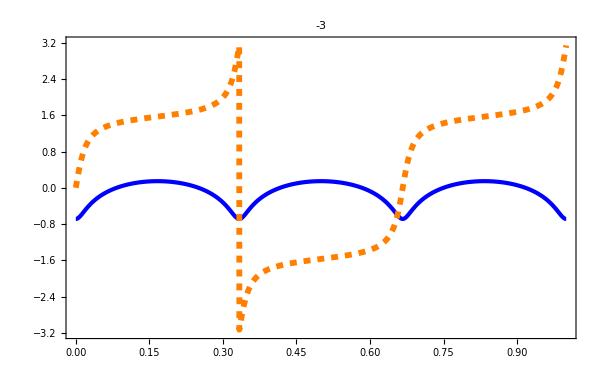
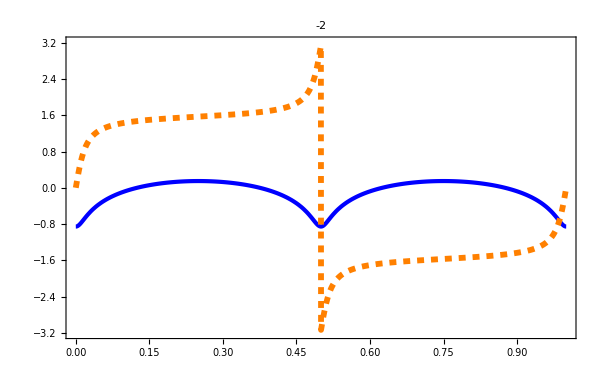
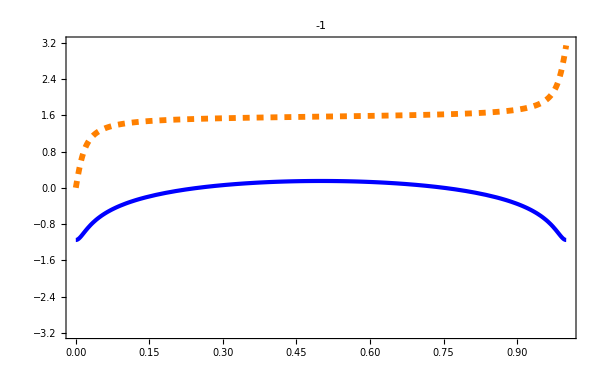
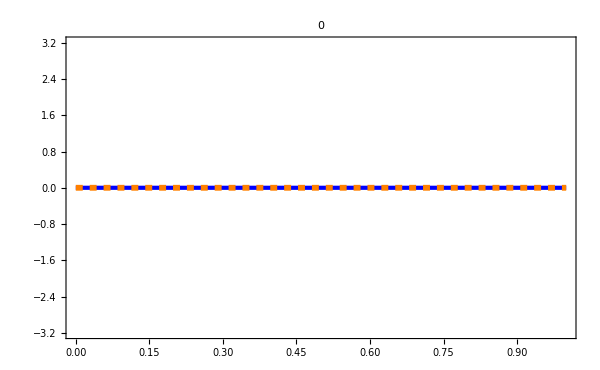
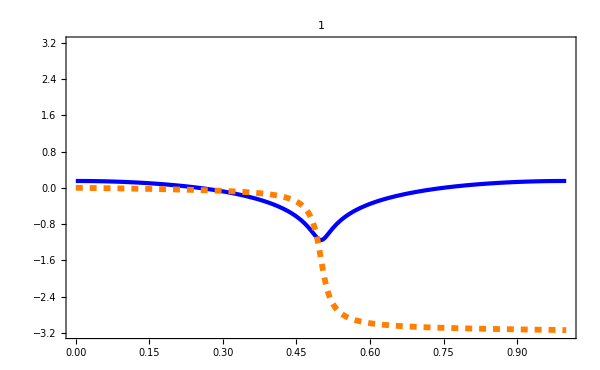
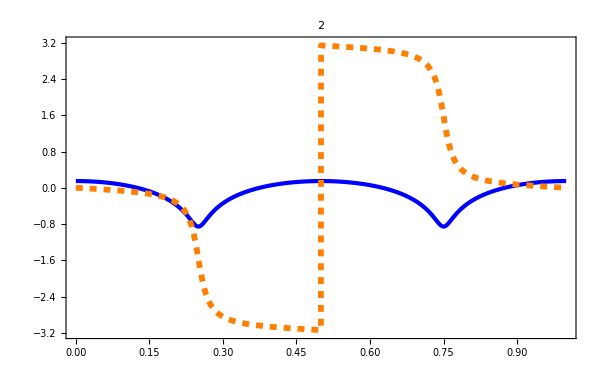
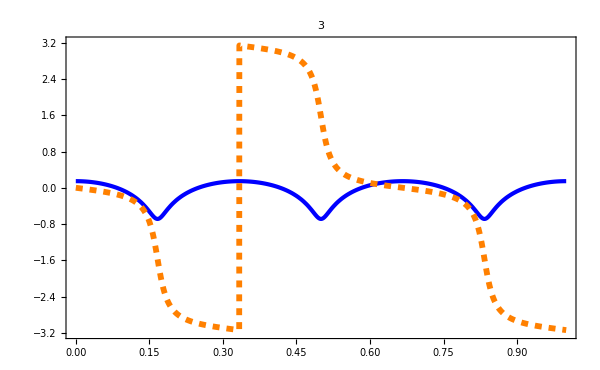

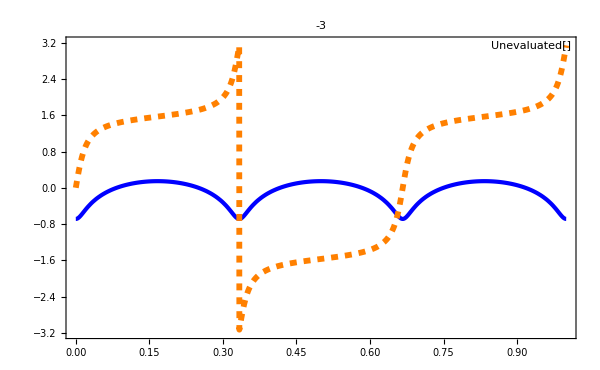

```mathematica
els = 3;
Table[
Plot[{Log10[Abs[cks[[i]]*xkplus[[i]]]/.q->20.],Arg[cks[[i]]*xkplus[[i]]]/.q->20.},{s,0,1},
PlotLegends->Placed[{"",""},{Right,Top}],
PlotLabel->Style[StringForm["`1`",i-Floor[(1/2)*Length[cks]]-1],Black],
PlotStyle->{{Blue,Thickness[0.005]},{Orange,Dashed,Thickness[0.007]}},
FrameLabel->{ Style["",45,Black],None},
FrameStyle->Black,Frame->True,ImageSize->600,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30},
PlotRange->{{0,1},{-3.2,3.2}}],
{i,Length[cks]-Floor[(1/2)*Length[cks]]-els,Length[cks]-Floor[(1/2)*Length[cks]]+els,1}
]
```

```mathematica
Table[
Plot[{Log10[Abs[ckstheo[[i]]*xkplus[[i]]]/.q->20.],Arg[ckstheo[[i]]*xkplus[[i]]]/.q->20.},{s,0,1},
PlotLegends->Placed[{"",""},{Right,Top}],
PlotLabel->Style[StringForm["`1`",i-Floor[(1/2)*Length[cks]]-1],Black],
PlotStyle->{{Blue,Thickness[0.005]},{Orange,Dashed,Thickness[0.007]}},
FrameLabel->{ Style["",45,Black],None},
FrameStyle->Black,Frame->True,ImageSize->600,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30},
PlotRange->{{0,1},{-3.2,3.2}}],
{i,Length[ckstheo]-Floor[(1/2)*Length[ckstheo]]-els,Length[ckstheo]-Floor[(1/2)*Length[ckstheo]]+els,1}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

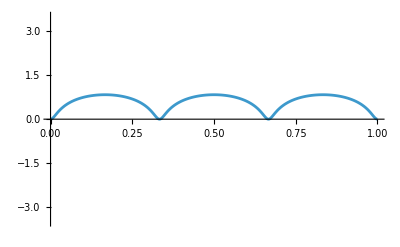
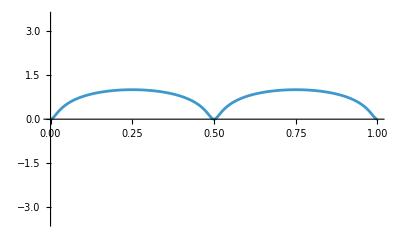
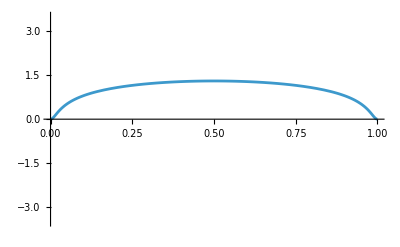
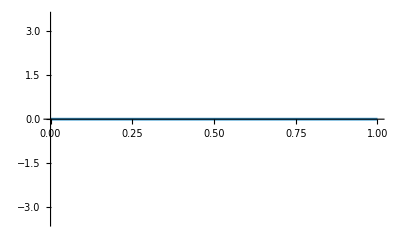
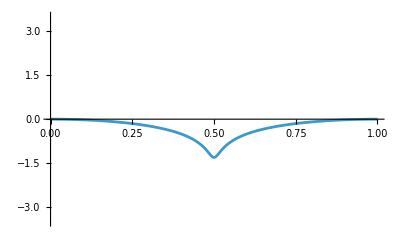
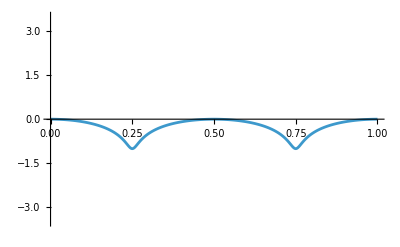
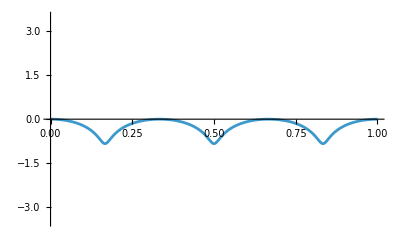

```mathematica
Table[
Plot[Log10[Abs[xkplus[[i]]]/.q->20],{s,0,1},PlotRange->{-3.5,3.5}],
{i,Length[cks]-Floor[(1/2)*Length[cks]]-els,Length[cks]-Floor[(1/2)*Length[cks]]+els,1}
]
```

## Stroboscopic plots

```mathematica
xcentroid =(cks*xkplus+cks*xkminus )/2;
```

```mathematica
ns = 20;
xcentroidstrobe = FullSimplify[Table[Re[xcentroid[[i]]*Exp[-2*I*Pi*j/ns]],{i,Length[xcentroid]},{j,0,ns}]/.q->20,Assumptions->s∈Reals];
```

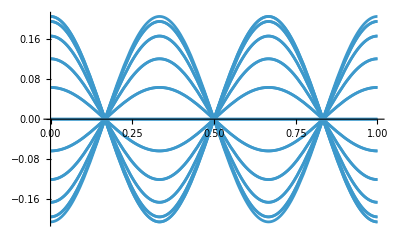
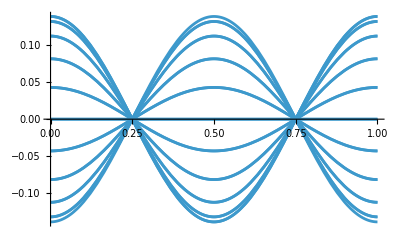
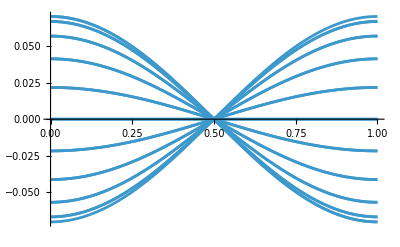
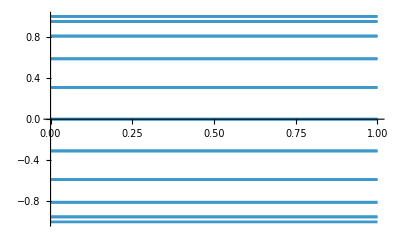
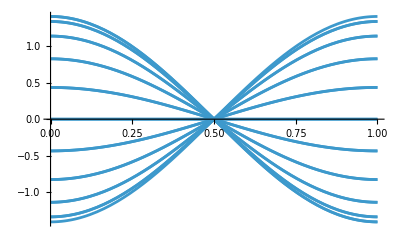
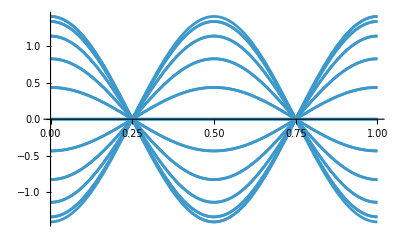
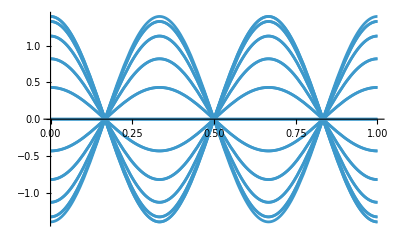

```mathematica
Table[
Plot[xcentroidstrobe[[i]],{s,0,1}],
{i,Length[xcentroid]-Floor[(1/2)*Length[xcentroid]]-els,Length[xcentroid]-Floor[(1/2)*Length[cks]]+els,1}
]
```

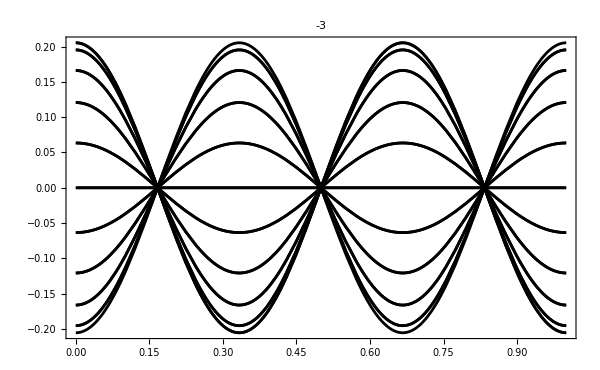
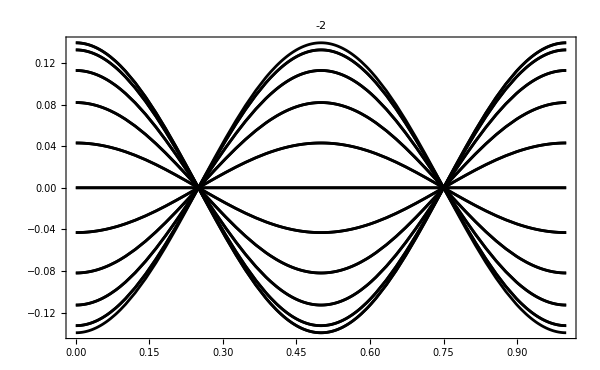
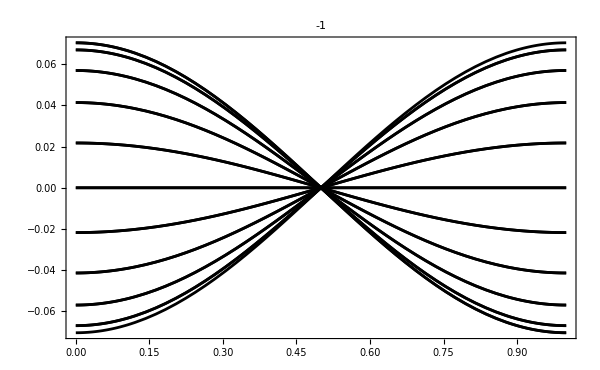
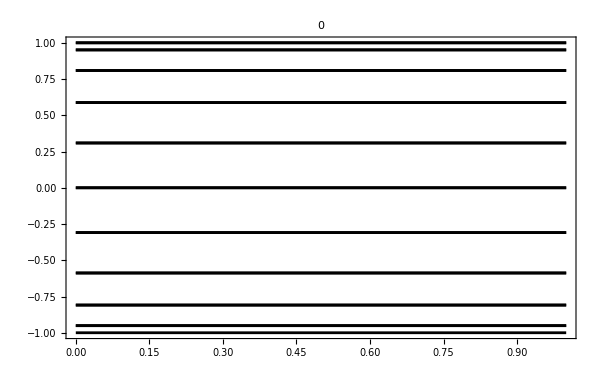
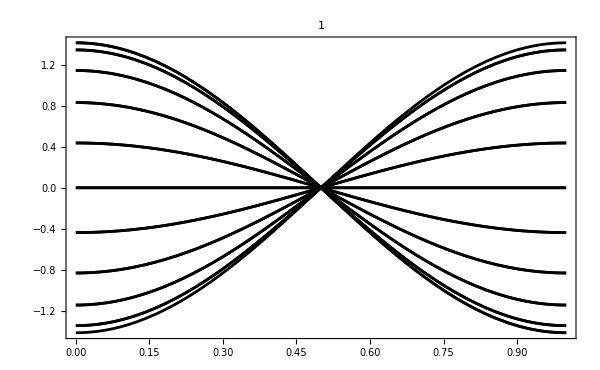
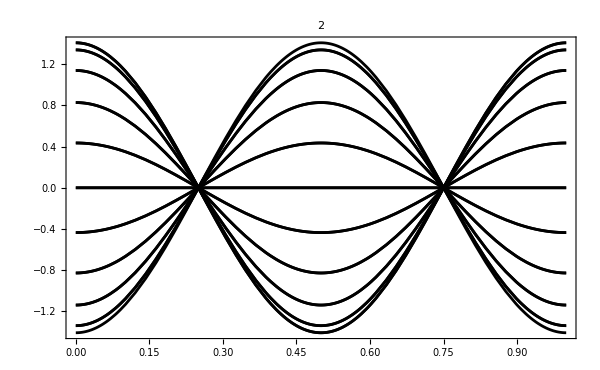
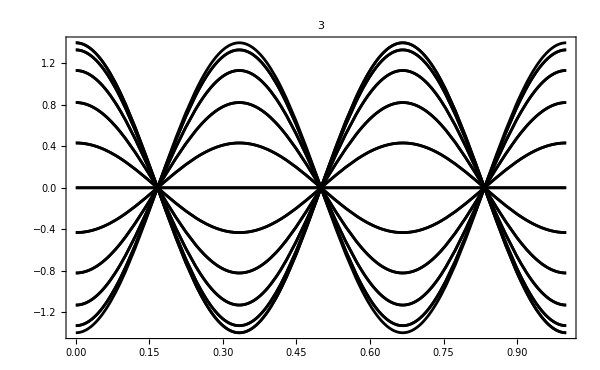

```mathematica
Table[
Plot[xcentroidstrobe[[i]],{s,0,1},
PlotRange->{{0,1},Automatic},
PlotStyle->{Black},
PlotLabel->Style[StringForm["`1`",i-Floor[(1/2)*Length[cks]]-1],Black],
FrameLabel->{ Style["",45,Black],Style["",45,Black]},
FrameStyle->Black,Frame->True,ImageSize->600,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->30}
],
{i,Length[xcentroid]-Floor[(1/2)*Length[xcentroid]]-els,Length[xcentroid]-Floor[(1/2)*Length[cks]]+els,1}
]
```